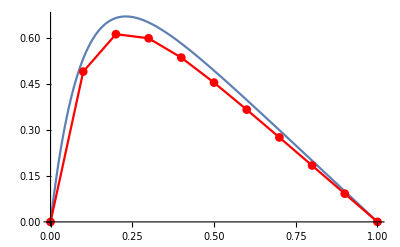

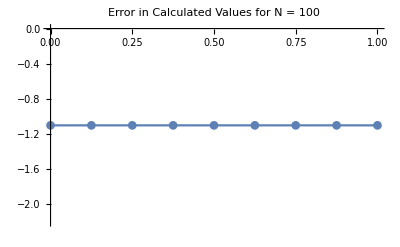

```mathematica
L=1;
n=11;
h=L/(n-1);
A=SparseArray[{Band[{2,1}]->1,Band[{1,1}]->-2,Band[{1,2}]->1},n-2];
f[x_]:=100 E^(-10x);
sol[x_]:=(1-ⅇ^(-10 x)-x+x/ⅇ^10);
fVec=N[Table[{-h^2 f[h*i]},{i,n-2}]];
data=Flatten[LinearSolve[A,fVec]];
data=Prepend[data,0];
data=Insert[data,0,n];
error = Table[Log10[Abs[N[(data[[i]]-sol[h*(i-1)])/sol[h*(i-1)]]]],{i,2,n-1}];
Show[
Plot[sol[x],{x,0,1},PlotRange->All],
ListLinePlot[data,DataRange->{0,L},PlotStyle->Red,PlotMarkers->Automatic]]
ListLinePlot[error, DataRange->{0,L},PlotMarkers->Automatic,PlotLabel->"Error in Calculated Values for N = 100"]
```

```mathematica
-2Log10[5]+1//N
```

-0.39794